# Billiards

The data is generated by a Haskell code.

## Functions, initialization cell

```mathematica
import[name_String]:=Module[{import,parsed},
import=Import[NotebookDirectory[]<>name,"Table"];
parsed=Flatten[ToExpression[StringReplace[#, {"["-> "{", "]"->"}","("-> "{", ")"->"}", "e"-> "*10^"} ]&/@#
],1]&@import
]

fitExp[data_,t_]:=a Exp[b t]/.FindFit[data,a Exp[b t],{a,b},t]
plot[data_,n_]:=Module[{},
Clear[t];
Print[fitExp[data[[1;;n]],t]];
Show[
ListPlot[{data[[1;;n]],data[[n+1;;-1]]},PlotRange->All],
Plot[Evaluate@fitExp[data[[1;;n]],t],{t,0,data[[-1,1]]}]
]
]
```

## sinai3

### Import data

```mathematica
{boundary, points}=import["p3.txt"];
{boundary, pointsP}=import["q3.txt"];
pointsPN=Flatten[import["qNew3.txt"],1]; 
dim=Length@boundary
```

3

### Original trajectory vs perturbed one

```mathematica
pointsFunc[i_]:=points[[1;;i]]
pointsPFunc[i_]:=pointsP[[1;;i]]

walls=Table[{-1,1}boundary[[i]],{i,1,Length@boundary}];
pointsFunc[i_]:=points[[1;;i]]
Manipulate[
Show[
ListPointPlot3D[pointsFunc[i], BoxRatios->{1, 1, 1},PlotRange->walls],
Graphics3D[Line@pointsFunc[i]],

 ListPointPlot3D[pointsPFunc[i], BoxRatios->{1, 1, 1},PlotRange->walls, PlotStyle->Red],
Graphics3D[{Red,Line@pointsPFunc[i]}],

Graphics3D[Sphere[{0,0,0}]]
]
,{i,1,Length@points,1}]
```

### New points on the old trajectory

```mathematica
Show[
ListPointPlot3D[pointsP, BoxRatios->{1, 1, 1},PlotRange->walls],
Graphics3D[Line@pointsP],

 ListPointPlot3D[pointsPN, BoxRatios->{1, 1, 1},PlotRange->walls, PlotStyle->Red],

Graphics3D[Sphere[{0,0,0}]]
]
```

-Graphics3D-

### Plot deviations

```mathematica
devs=Flatten[import["deviations3.txt"],1];
```

0.0000223062 ⅇ^(1.06265 t)

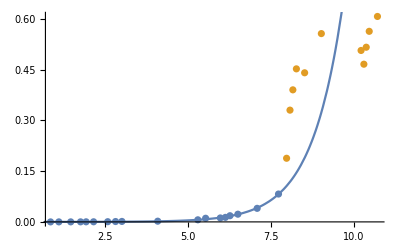

```mathematica
plot[devs,18]
```